# QKT

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Geometric floquet\\QKT_full.wl"];
```

```mathematica
LaunchKernels[14];
```

```mathematica
Names["QKT`*"]
```

{ClassicalMapeo,ClassicalStep,ClassicalToDisk,ClassicalToSphere,COEAsymptoticSigma2,COESFFAnalytical,CompileLevelCounter,CompileSFF,ComputeSigma2Sliding,EnsembleSFF,EnsembleSigma2,EvaluateSpectrumSigma2,Floq,Floqb,Floqbn,Floqn,Floqsym,FluctuationPowerSpectrum,GenerateCOEEnsemble,generateCoherentStateCompiler,GenerateQKTEnsemble,generateSpinOperators,GetFluctuations,GetQKTParityEigensystem,GetQKTParitySpectra,IntWignerCOE,IPR,LengthSpectrum,MeanLevelSpacingRatio,NNSpacings,ParitySectorIndices,PoolSpacingRatios,PoolSpacings,PrCOE,PrCUE,PrPoisson,RandomCOESpectrum,SingleSFF,SingleSpectrumSigma2,UnfoldLinear,ValidateUnfolding,WignerCOE}

```mathematica
Clear[SplitQKTParity];
SplitQKTParity[Op_?MatrixQ]:=Module[{dim,Jval,OpEven,OpOdd},
(*Calculate J from the dimension of the matrix (dim=2J+1)*)
dim=Length[Op];
Jval=(dim-1)/2;
If[EvenQ[Jval],
(*If J is EVEN:Row 1 (M=J) is Even Parity*)
OpEven=Op[[1;; ;;2,1;; ;;2]];
OpOdd=Op[[2;; ;;2,2;; ;;2]];,
(*If J is ODD:Row 1 (M=J) is Odd Parity*)
OpEven=Op[[2;; ;;2,2;; ;;2]];
OpOdd=Op[[1;; ;;2,1;; ;;2]];];
{OpEven,OpOdd}];
```

## QKT

```mathematica
(*Floquet parameters*)
J=500;
α=0.84;
k=3.0;
```

```mathematica
(*Generates all J operators, Jx, Jy, Jz, Jx^2*)
ops=generateSpinOperators[J];
```

```mathematica
?GetQKTParityEigensystem
```

```mathematica
data=GetQKTParityEigensystem[J,α,k];
```

```mathematica
{eigenvalM,eigenvalm}={data["Even","Quasienergies"],data["Odd","Quasienergies"]};
{neweigenvecM,neweigenvecm}={data["Even","FullVectors"],data["Odd","FullVectors"]};
```

```mathematica
{MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]}
```

{0.449867,0.439721}

```mathematica
(*Unfolding, only works for uniform density of states in the chaotic regime COE*)
phases=Sort[Arg[eigenvalM]];
n=Length[phases];
unfolded=phases*(n/(2*Pi));
spacings=Differences[unfolded];
meanSpacing=Mean[spacings];
spacings=spacings/meanSpacing;
```

```mathematica
poisson[s_]:=Exp[-s];
wignerDyson[s_]:=(Pi*s/2)*Exp[-(Pi*s^2)/4];
```

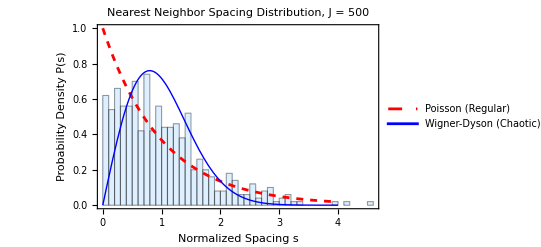

```mathematica
Show[Histogram[spacings,{0.1},"PDF",ChartStyle->LightBlue,Frame->True,FrameLabel->{"Normalized Spacing s","Probability Density P(s)"},PlotLabel->"Nearest Neighbor Spacing Distribution, J = "<>ToString[J]],Plot[{poisson[s],wignerDyson[s]},{s,0,4},PlotStyle->{{Red,Dashed},{Blue,Thick}},PlotLegends->{"Poisson (Regular)","Wigner-Dyson (Chaotic)"}]]
```

## Average energy

```mathematica
(*Floquet parameters*)
J=500;
α=0.84;
k=3.0;
```

```mathematica
ops=generateSpinOperators[J];
(* Floquet: original with twist along Sz *)
Clear[Uk,U0,F];
Uk[k_] := MatrixExp[(-I k/(2 J)) ops[[4]]];
U0[α_] := MatrixExp[(-I α) ops[[3]]];
F[α_,k_] :=Uk[ k].U0[α];
Clear[V];
V[α_,k_]:=(k/(2J))ConjugateTranspose[U0[α]].ops[[4]].U0[α]+α*ops[[3]];
```

```mathematica
Print["Computing Floquet matrix by parity sector..."];
data=GetQKTParityEigensystem[J,α,k];
{eigenvalM,eigenvalm}={data["Even","Quasienergies"],data["Odd","Quasienergies"]};
{eigenvecM,eigenvecm}={data["Even","Vectors"],data["Odd","Vectors"]};
{neweigenvecM,neweigenvecm}={data["Even","FullVectors"],data["Odd","FullVectors"]};
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

Computing Floquet matrix by parity sector...

```mathematica
Vop=V[α,k];
{szM,szm}=SplitQKTParity[V[α,k]];
szExpectationsM=Map[#.szM.ConjugateTranspose[#]&,eigenvecM];
szExpectationsm=Map[#.szm.ConjugateTranspose[#]&,eigenvecm];
```

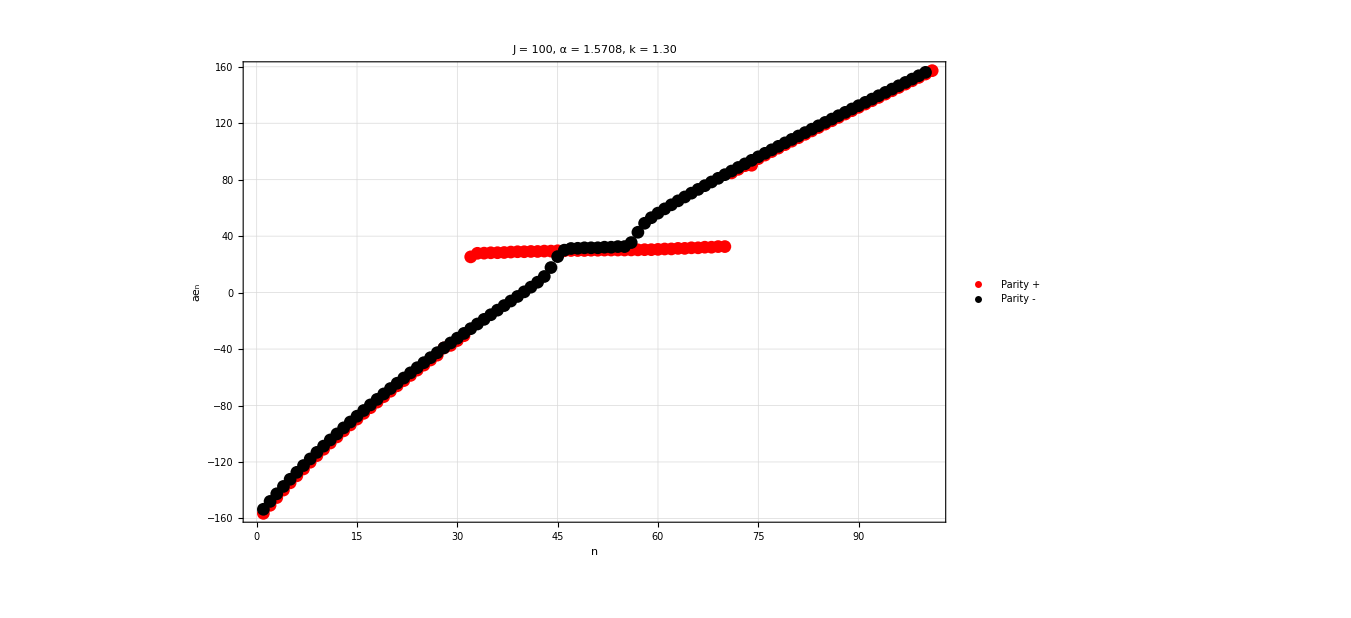

```mathematica
plot=ListPlot[{Sort[Chop[szExpectationsM]],Sort[Chop[szExpectationsm]]},PlotStyle->{Red,Black},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Rotate[Style["ae_n",35,Black],-90 Degree]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},ImageSize->1000]
Export["plateu1_alpha_pihalf_J_"<>ToString[J]<>"_.png",plot];
```

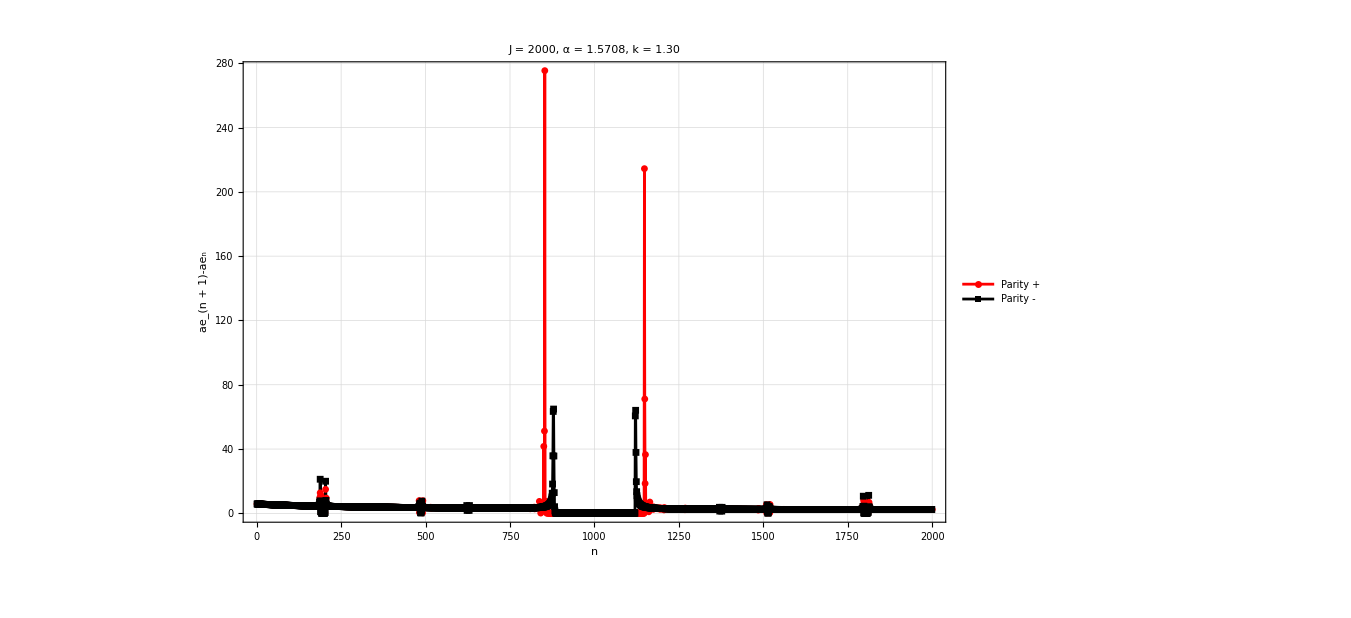

differences1_alpha_pihalf_J_2000_.png

```mathematica
newM=Sort[Chop[szExpectationsM]];
newm=Sort[Chop[szExpectationsm]];
plot2=ListPlot[{Differences[newM],Differences[newm]},PlotStyle->{Red,Black},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Style["ae_(n + 1)-ae_n",35,Black]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},Joined->True,PlotMarkers->{Automatic, Small},ImageSize->1000]
Export["differences1_alpha_pihalf_J_"<>ToString[J]<>"_.png",plot2]
```

## IPR & Husimis

```mathematica
(*Resolution of the grid for the phase space*)
radius=2;
delta=0.025;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPointsRaw=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*Keep only those inside disk*)
region=Select[gridPointsRaw,Norm[#]<radius&];
region//Dimensions
```

{20069,2}

```mathematica
Print["Generating coherent states over ",Length[region]," points..."];
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

Generating coherent states over 20069 points...

```mathematica
(*Sorting with respect the average energy*)
ae=Chop[Map[#.Vop.ConjugateTranspose[#]&,neweigenvec]];
```

```mathematica
ordering=Ordering[ae];
(*Sort eigenvectors and expectations accordingly*)
eigenvecsSorted=neweigenvec[[ordering]];
eigenvalSorted=neweigenval[[ordering]];
```

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[eigenvecsSorted].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Projecting states into Floquet basis...

Computing IPRs...

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
```

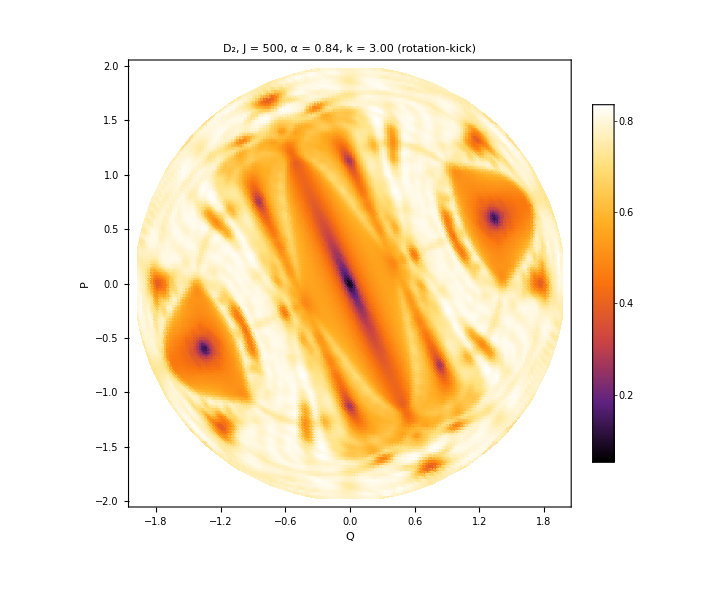

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>" (rotation-kick)",25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,Background->White]
```

```mathematica
dir="HusimiPlots";
If[!DirectoryQ[dir],CreateDirectory[dir]];
```

```mathematica
husimiValues=Abs[overlaps]^2;
husimiValuesSorted=husimiValues;
```

```mathematica
(*Set parameters, 2J+1 Husimis in total*)
numEigenstates=2J+1; 
plots=Table[
Module[{husimiList,plot},
husimiList=MapThread[Append,{region,husimiValuesSorted[[q]]}];
plot=ListDensityPlot[husimiList,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["AE Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", Eigenvec_q = "<>ToString[q],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->1];
Export[FileNameJoin[{dir,"AE_Husimi_J_"<>ToString[J]<>"_q"<>ToString[q]<>".png"}],plot];
plot],{q,numEigenstates}];
```

```mathematica
ae//Sort
```

{-23.7541,-15.6602,-10.8053,-9.90192,-5.64294,-2.39631,0.109928,2.07873,2.16826,2.43,2.98262,2.98384,3.66659,3.88743,3.88746,4.61932,4.61933,5.12387,5.20698,5.20699,5.6674,5.6677,6.00415,6.01507,6.17422,6.28965,6.2964,6.36884,6.59838,6.62782,6.84551,7.46039,8.60166,9.62781,10.7949,12.2561,14.1865,15.5611,16.8202,20.5642,26.1252}

## Sorted Husimis

```mathematica
(*---Fixed parameters---*)
J=30;
α=Pi/2.;
δk=0.01;  (*adjust as needed*)
kList=Range[0.1,1.2,δk];
kList//Length
```

111

```mathematica
dimM=J+1;
dimm=J;
posM=Range[1,2 J+1,2];
posm=Range[2,2 J,2];

(*---Spin operators (once)---*)
ops=generateSpinOperators[J];

(*---Phase-space grid (once)---*)
radius=2;
delta=0.015;
region=Select[Flatten[Table[{x,y},{x,Range[-radius,radius,delta]},{y,Range[-radius,radius,delta]}],1],Norm[#]<radius&];
Print["Grid points: ",Length[region]];

(*---Coherent states (once)---*)
coherentStateGenerator=generateCoherentStateCompiler[];
Print["Generating coherent states..."];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"];
```

Grid points: 55828

Generating coherent states...

```mathematica
(*---Folder structure---*)
rootDir="HusimiK_J_30";
posDir=FileNameJoin[{rootDir,"PositiveParity"}];
negDir=FileNameJoin[{rootDir,"NegativeParity"}];
If[!DirectoryQ[#],CreateDirectory[#,CreateIntermediateDirectories->True]]&/@{rootDir,posDir,negDir};
Table[With[{d=FileNameJoin[{posDir,"Husimi_"<>IntegerString[q,10,2]}]},If[!DirectoryQ[d],CreateDirectory[d]]],{q,dimM}];
Table[With[{d=FileNameJoin[{negDir,"Husimi_"<>IntegerString[q,10,2]}]},If[!DirectoryQ[d],CreateDirectory[d]]],{q,dimm}];
```

```mathematica
(*---Helpers---*)
KLabel[k_]:=StringReplace[ToString[NumberForm[N[k],{4,2}]],"."->"p"];

ComputeSortedEigensystem[k_]:=Module[{Uk,U0,F,matM,matm,eigenvalM,eigenvecM,eigenvalm,eigenvecm,neweigenvecM,neweigenvecm,neweigenvec,neweigenval,Vop,ae,ordering},Uk=MatrixExp[(-I k/(2 J)) ops["Sx2"]];
U0=MatrixExp[(-I α) ops["Sz"]];
F=U0.Uk;
matM=F[[1;; ;;2,1;; ;;2]];
matm=F[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
neweigenvecM=Table[Riffle[eigenvecM[[j]],ConstantArray[0.,J]],{j,dimM}];
neweigenvecm=Table[Riffle[ConstantArray[0.,J+1],eigenvecm[[j]]],{j,dimm}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
Vop=(k/(2 J)) ops["Sx2"]+α*ConjugateTranspose[Uk].ops["Sz"].Uk;
ae=Chop[Map[#.Vop.ConjugateTranspose[#]&,neweigenvec]];
ordering=Ordering[ae];
<|"eigenvecsSorted"->neweigenvec[[ordering]],"ae"->ae[[ordering]],"originIndices"->ordering|>];

SplitByParity[originIndices_]:={Flatten[Position[MemberQ[posM,#]&/@originIndices,True]],Flatten[Position[MemberQ[posm,#]&/@originIndices,True]]};

HusimiPlot[overlaps_,idx_,label_]:=Module[{husimiList},husimiList=MapThread[Append,{region,Abs[overlaps[[idx]]]^2}];
ListDensityPlot[husimiList,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style[label,20,Black],ImageSize->800,AspectRatio->1,Frame->True,InterpolationOrder->1,FrameLabel->{Style["Q",35,Black],Rotate[Style["P",35,Black],-90 Degree]},LabelStyle->Directive[25,Black]]];
```

```mathematica
(*---Distribute to subkernels---*)
DistributeDefinitions[J,α,dimM,dimm,posM,posm,ops,statesCompiled,region,posDir,negDir,KLabel,ComputeSortedEigensystem,SplitByParity,HusimiPlot];
```

```mathematica
(*---Main loop---*)
Print["Starting k sweep..."];
ParallelDo[
Print["  k = ",k];
sys=ComputeSortedEigensystem[k];
overlaps=Conjugate[sys["eigenvecsSorted"]].Transpose[statesCompiled];
{aePosM,aePosm}=SplitByParity[sys["originIndices"]];

Do[With[{idx=aePosM[[r]],fdir=FileNameJoin[{posDir,"Husimi_"<>IntegerString[r,10,2]}],label="PositiveParity, rank "<>ToString[r]<>", J="<>ToString[J]<>", α="<>ToString[NumberForm[N[α],{4,2}]]<>", k="<>ToString[NumberForm[k,{4,2}]]<>", ae="<>ToString[NumberForm[sys["ae"][[aePosM[[r]]]],{6,3}]]},Export[FileNameJoin[{fdir,"k_"<>KLabel[k]<>".png"}],HusimiPlot[overlaps,idx,label]]],{r,dimM}];
Do[With[{idx=aePosm[[r]],fdir=FileNameJoin[{negDir,"Husimi_"<>IntegerString[r,10,2]}],label="NegativeParity, rank "<>ToString[r]<>", J="<>ToString[J]<>", α="<>ToString[NumberForm[N[α],{4,2}]]<>", k="<>ToString[NumberForm[k,{4,2}]]<>", ae="<>ToString[NumberForm[sys["ae"][[aePosm[[r]]]],{6,3}]]},Export[FileNameJoin[{fdir,"k_"<>KLabel[k]<>".png"}],HusimiPlot[overlaps,idx,label]]],{r,dimm}],{k,kList}];
Print["Done. Files saved under: ",rootDir];
```

# Average energy

## Average energy

```mathematica
(*Floquet parameters*)
J=2000;
α=0.84;
k=1.3;
```

```mathematica
ops=generateSpinOperators[J];
(* Floquet: original with twist along Sz *)
Clear[Uk,U0,F];
Uk[k_] := MatrixExp[(-I k/(2 J)) ops[[4]]];
U0[α_] := MatrixExp[(-I α) ops[[3]]];
F[α_,k_] :=Uk[ k]. U0[α];
Clear[V];
(*V[α_,k_]:=(k/(2J))ConjugateTranspose[U0[α]].ops[[4]].U0[α]+α*ops[[3]];*)
V[α_,k_]:=α*ops[[3]];
```

```mathematica
data=GetQKTParityEigensystem[J,α,k];
{eigenvalM,eigenvalm}={data["Even","Quasienergies"],data["Odd","Quasienergies"]};
{eigenvecM,eigenvecm}={data["Even","Vectors"],data["Odd","Vectors"]};
{neweigenvecM,neweigenvecm}={data["Even","FullVectors"],data["Odd","FullVectors"]};
```

```mathematica
Vop=V[α,k];
{szM,szm}=SplitQKTParity[V[α,k]];
szExpectationsM=(1/J)Map[#.szM.ConjugateTranspose[#]&,eigenvecM];
szExpectationsm=(1/J)Map[#.szm.ConjugateTranspose[#]&,eigenvecm];
```

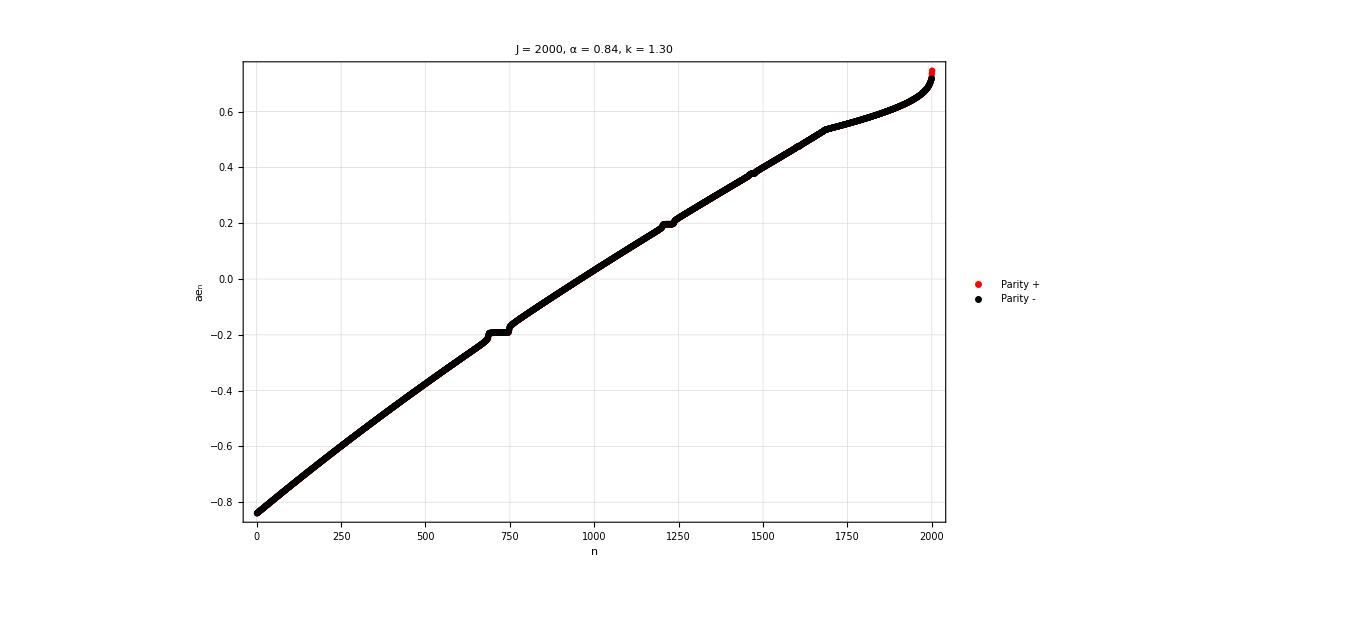

```mathematica
plot=ListPlot[{Sort[Chop[szExpectationsM]],Sort[Chop[szExpectationsm]]},PlotStyle->{Red,Black},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Rotate[Style["ae_n",35,Black],-90 Degree]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},ImageSize->1000]
```

```mathematica
newM=Sort[Chop[szExpectationsM]];
newm=Sort[Chop[szExpectationsm]];
```

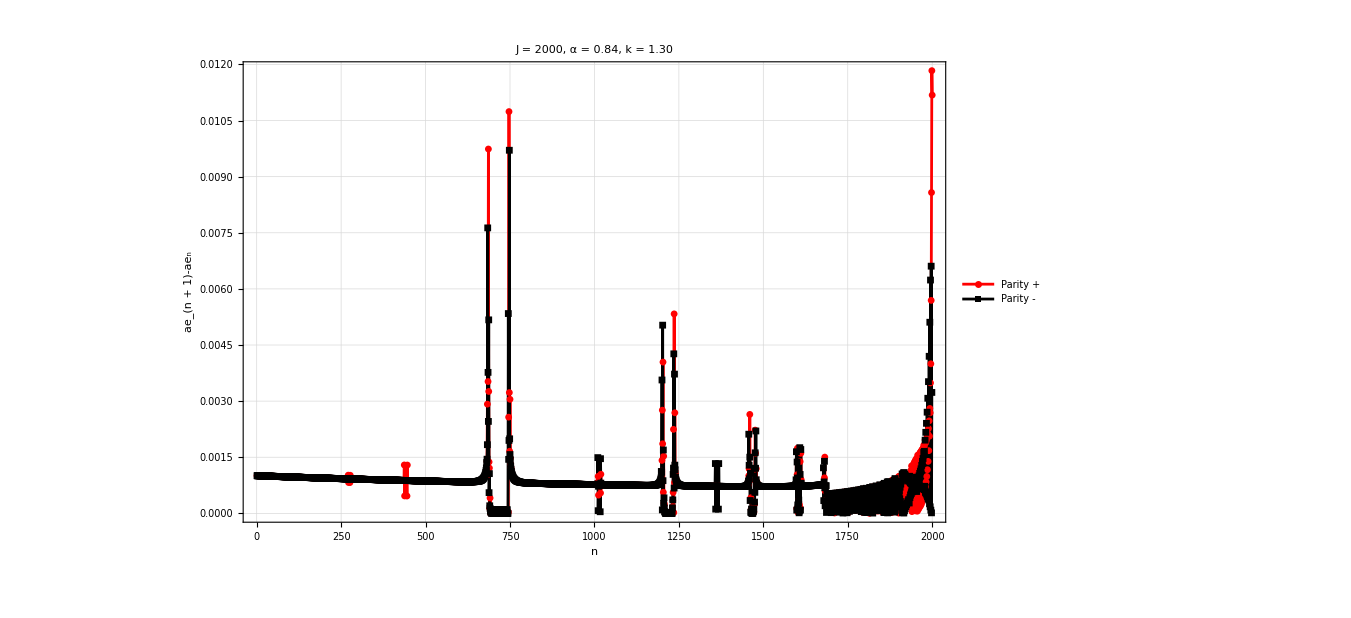

```mathematica
plot2=ListPlot[{Differences[newM],Differences[newm]},PlotStyle->{Red,Black},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Style["ae_(n + 1)-ae_n",35,Black]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},Joined->True,PlotMarkers->{Automatic, Small},ImageSize->1000]
```

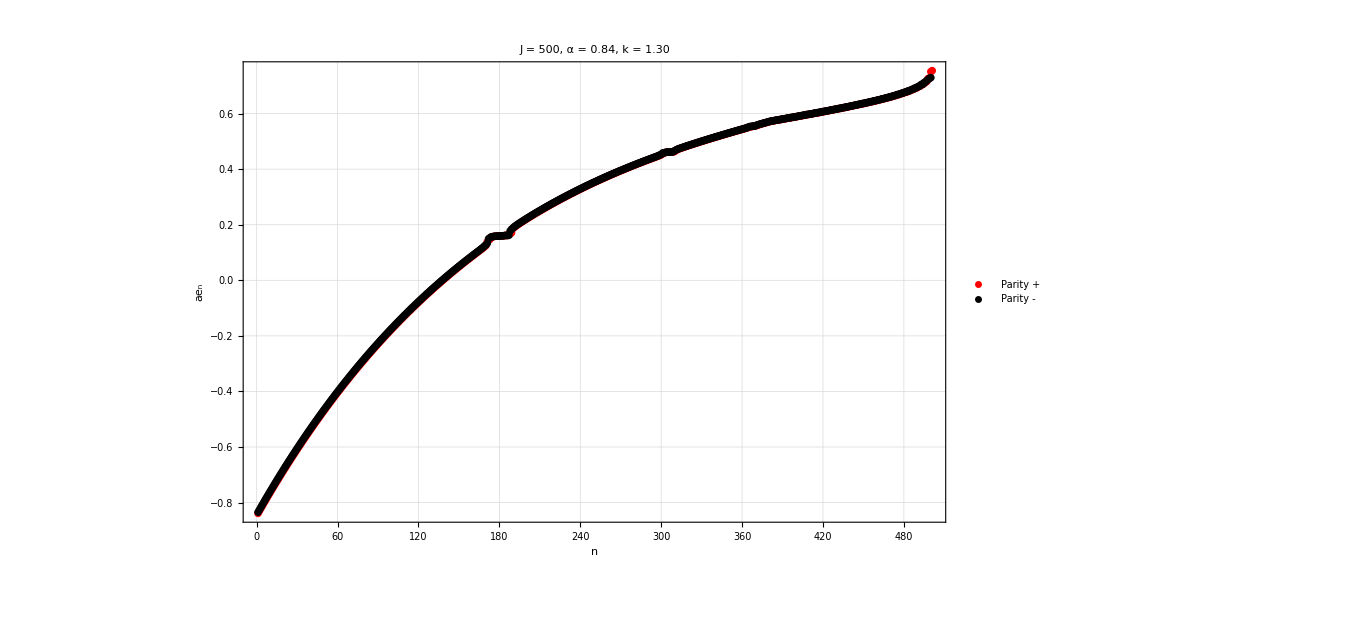

```mathematica
plot=ListPlot[{Sort[Chop[szExpectationsM]],Sort[Chop[szExpectationsm]]},PlotStyle->{Red,Black},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Rotate[Style["ae_n",35,Black],-90 Degree]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},ImageSize->1000]
```

```mathematica
newM=Sort[Chop[szExpectationsM]];
newm=Sort[Chop[szExpectationsm]];
```

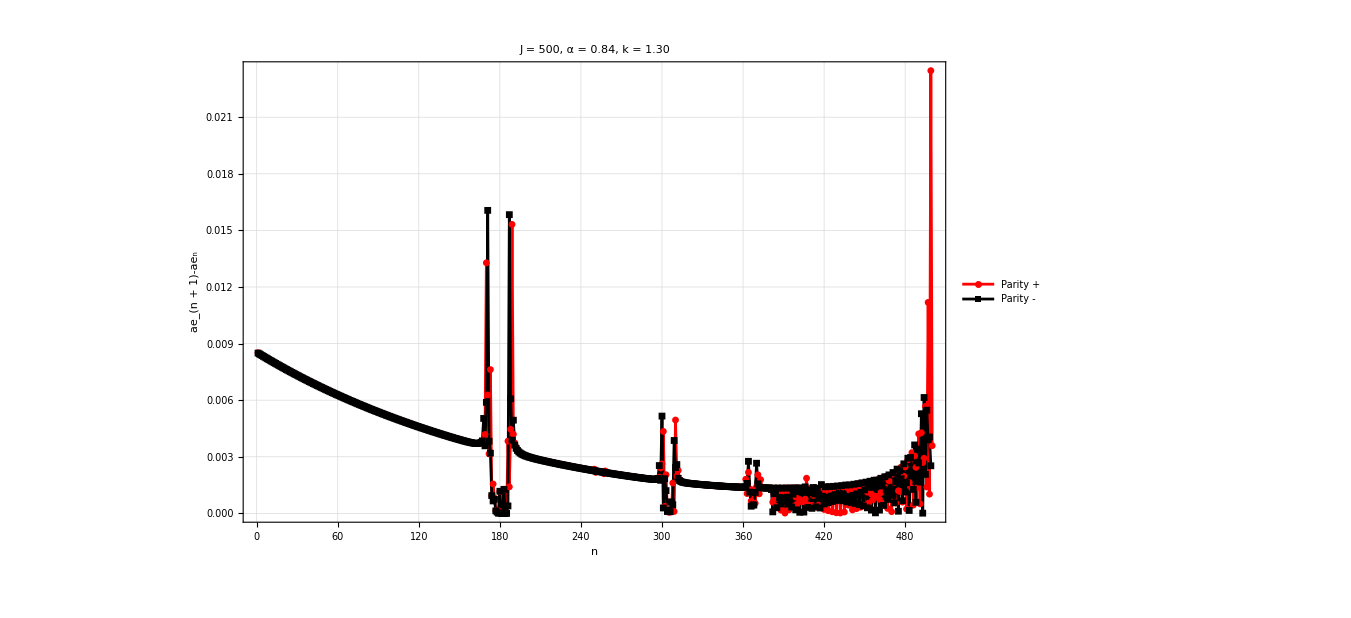

```mathematica
plot2=ListPlot[{Differences[newM],Differences[newm]},PlotStyle->{Red,Black},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Style["ae_(n + 1)-ae_n",35,Black]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},Joined->True,PlotMarkers->{Automatic, Small},ImageSize->1000]
```

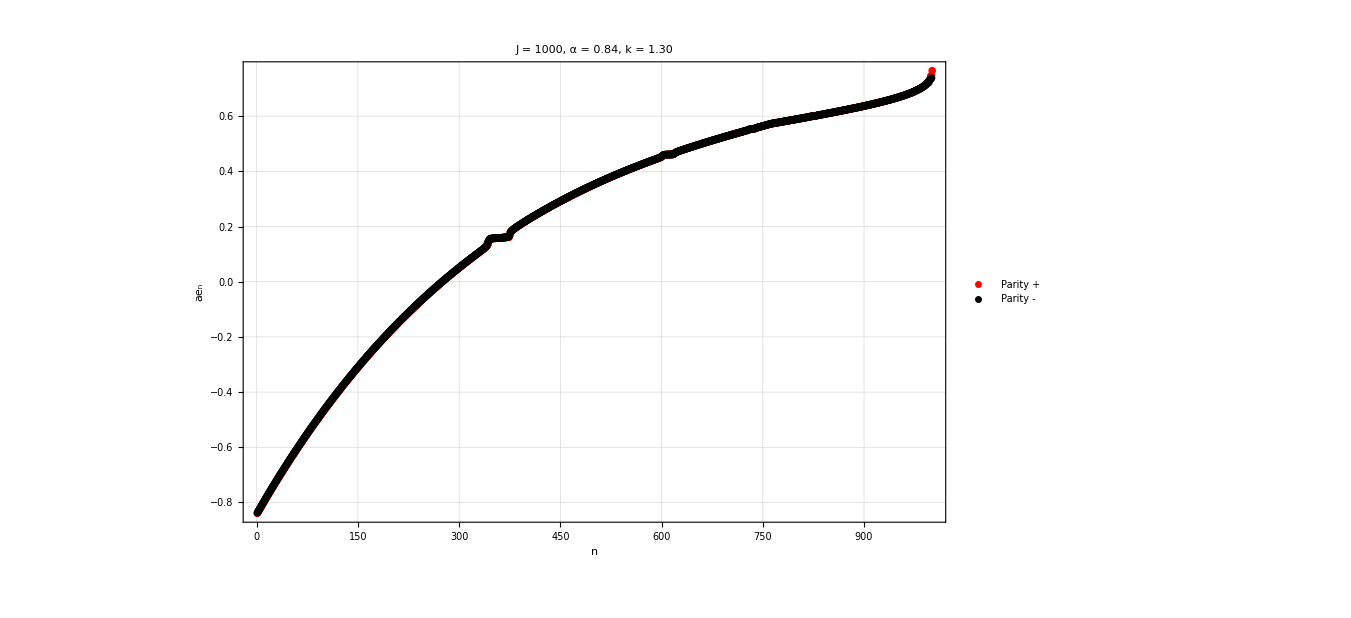

```mathematica
plot=ListPlot[{Sort[Chop[szExpectationsM]],Sort[Chop[szExpectationsm]]},PlotStyle->{Red,Black},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Rotate[Style["ae_n",35,Black],-90 Degree]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},ImageSize->1000]
```

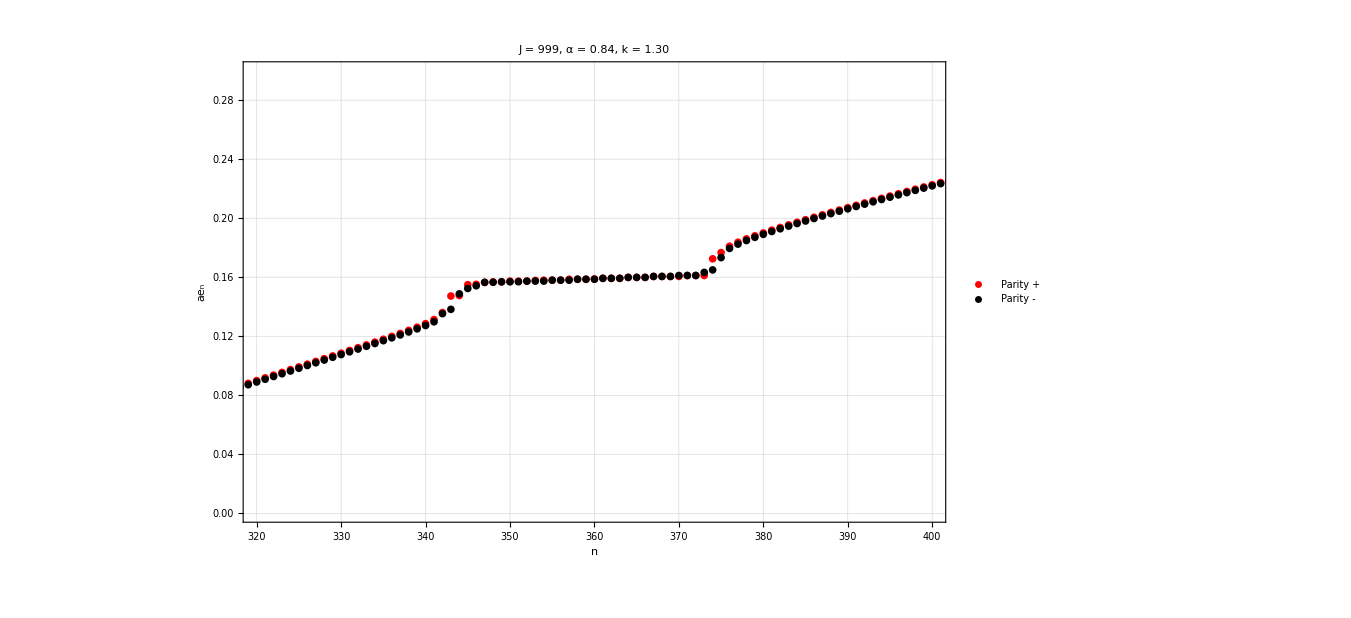

```mathematica
plot=ListPlot[{Sort[Chop[szExpectationsM]],Sort[Chop[szExpectationsm]]},PlotStyle->{Red,Black},PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Rotate[Style["ae_n",35,Black],-90 Degree]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},ImageSize->1000,PlotRange->{{320,400},{0,0.3}}]
```

```mathematica
newM=Sort[Chop[szExpectationsM]];
newm=Sort[Chop[szExpectationsm]];
```

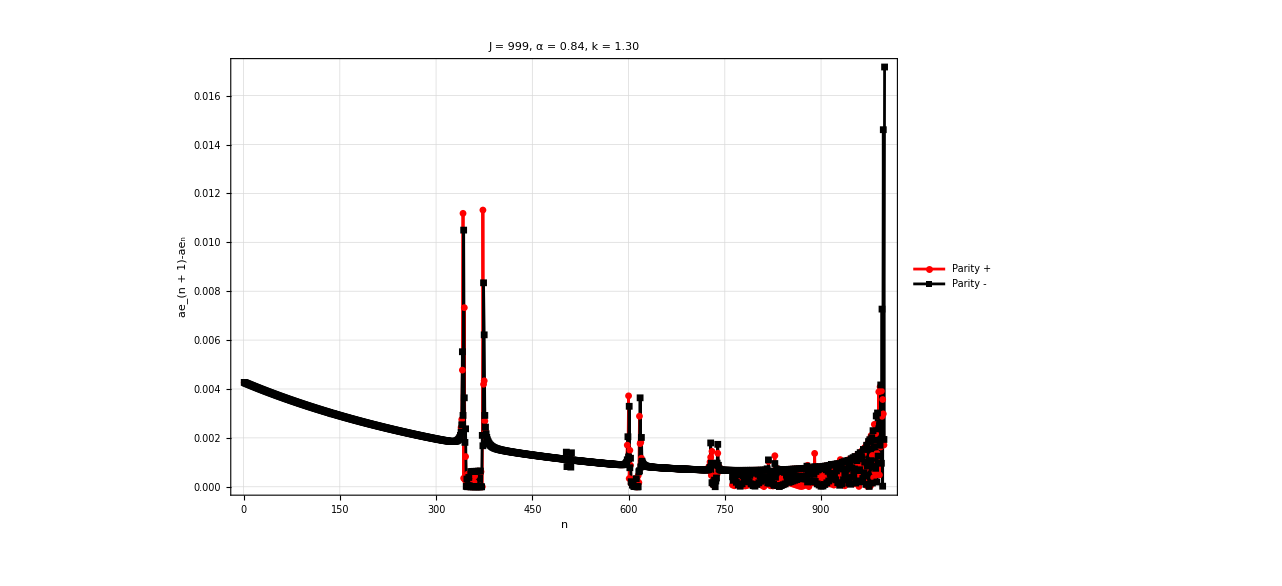

```mathematica
plot2=ListPlot[{Differences[newM],Differences[newm]},PlotStyle->{Red,Black},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Style["ae_(n + 1)-ae_n",35,Black]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},Joined->True,PlotMarkers->{Automatic, Small},ImageSize->1000]
```

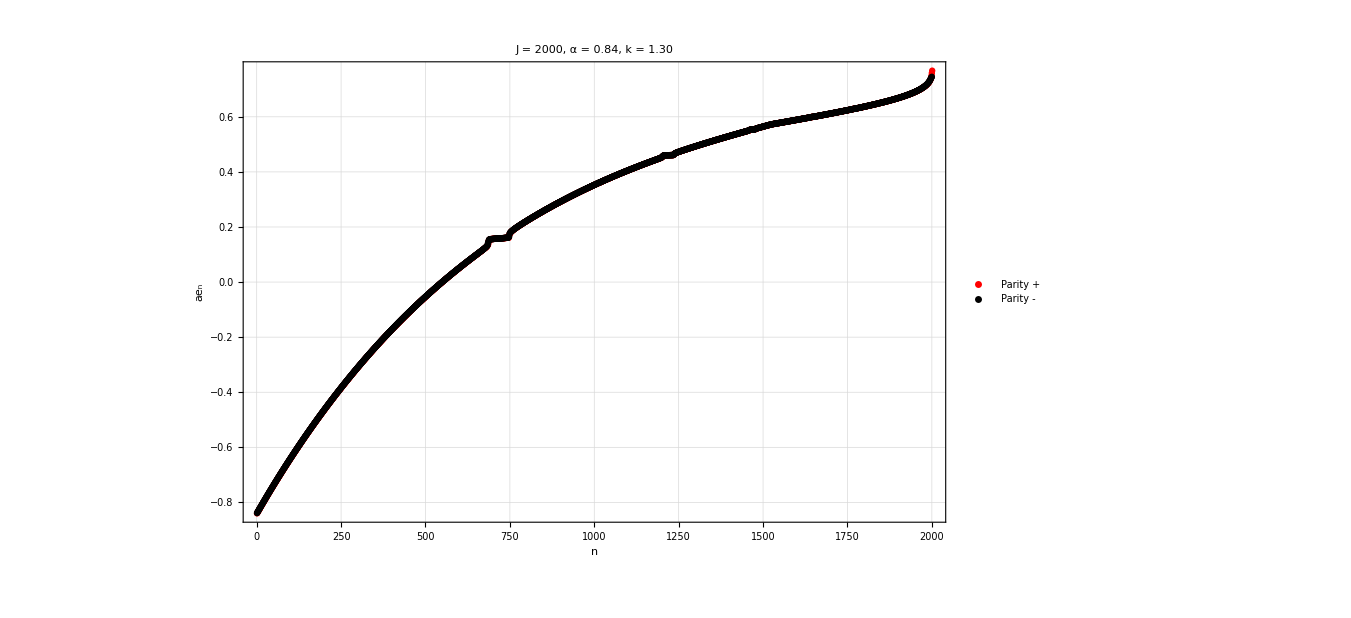

```mathematica
plot=ListPlot[{Sort[Chop[szExpectationsM]],Sort[Chop[szExpectationsm]]},PlotStyle->{Red,Black},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Rotate[Style["ae_n",35,Black],-90 Degree]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},ImageSize->1000]
```

```mathematica
newM=Sort[Chop[szExpectationsM]];
newm=Sort[Chop[szExpectationsm]];
```

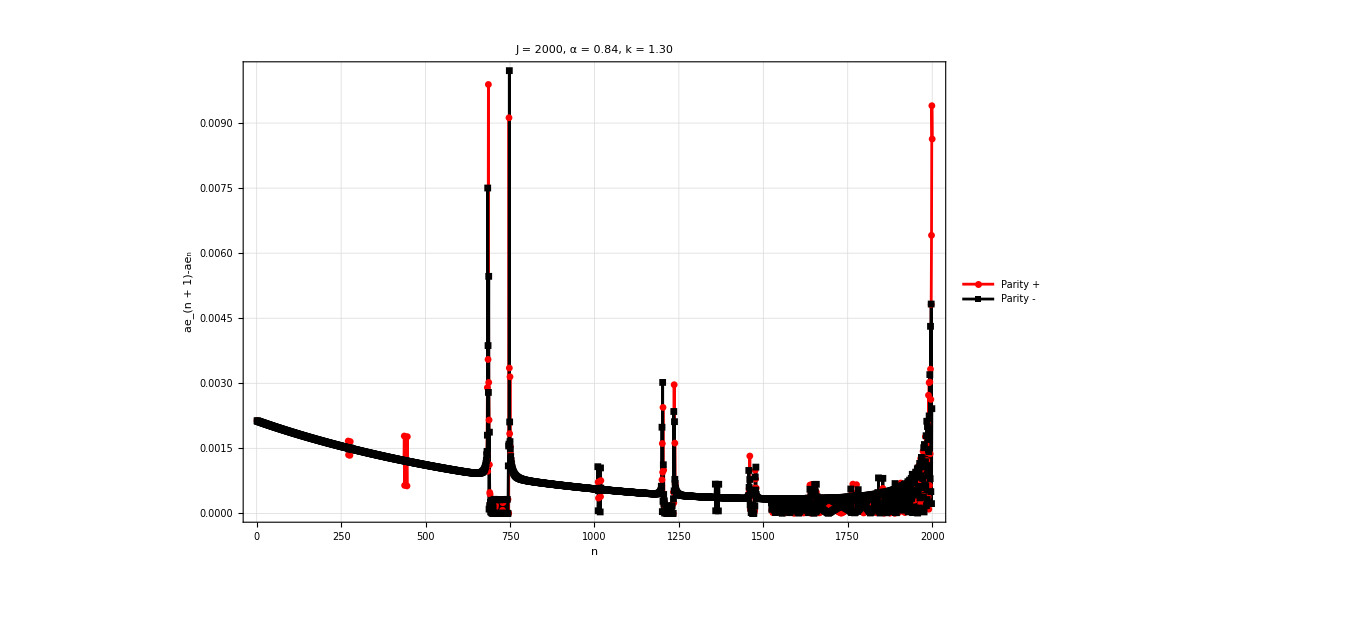

```mathematica
plot2=ListPlot[{Differences[newM],Differences[newm]},PlotStyle->{Red,Black},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]],25,Black],FrameLabel->{Style["n",35,Black],Style["ae_(n + 1)-ae_n",35,Black]},LabelStyle->Directive[25,Black],Frame->True,Background->White,PlotLegends->{Style["Parity +"],Style["Parity -"]},Joined->True,PlotMarkers->{Automatic, Small},ImageSize->1000]
```

## Average density of states

```mathematica
(*Floquet parameters*)
J=1000;
α=0.84;
```

```mathematica
k=1.3;
```

```mathematica
ops=generateSpinOperators[J];
```

```mathematica
(* Floquet: original with twist along Sz *)
Clear[Uk,U0,F];
Uk[k_] := MatrixExp[(-I k/(2 J)) ops[[4]]];
U0[α_] := MatrixExp[(-I α) ops[[3]]];
F[α_,k_] := U0[α].Uk[ k];
```

```mathematica
Clear[V];
V[α_,k_]:=(k/(2J))ops[[4]]+α*ConjugateTranspose[Uk[k]].ops[[3]].Uk[k];
```

```mathematica
Vop=V[α,k];
```

```mathematica
Clear[mat];
Print["Computing matrix by parity sector..."];
mat=Vop;
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

Computing matrix by parity sector...

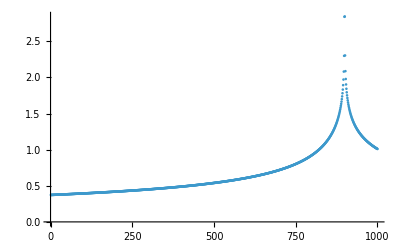

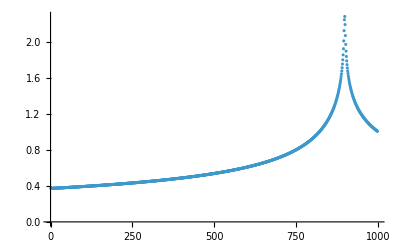

```mathematica
ListPlot[1/Differences[Sort[Chop[eigenvalM]]],PlotRange->All]
ListPlot[1/Differences[Sort[Chop[eigenvalm]]],PlotRange->All]
```

# Spectrum Hf as a function of α

## ae

```mathematica
(*Floquet parameters*)
J=50;
```

```mathematica
ops=generateSpinOperators[J];
(* Floquet: original with twist along Sz *)
Clear[Uk,U0,F];
Uk[k_] := MatrixExp[(-I k/(2 J)) ops[[4]]];
U0[α_] := MatrixExp[(-I α) ops[[3]]];
F[α_,k_] :=Uk[ k]. U0[α];
Clear[V];
V[α_,k_]:=(k/(2J))ConjugateTranspose[U0[α]].ops[[4]].U0[α]+α*ops[[3]];
```

```mathematica
α=ArcTan[2.];
```

```mathematica
alist=Range[62,64,0.0005];
alist//Length
```

4001

```mathematica
Clear[SplitQKTParity];
SplitQKTParity[Op_?MatrixQ]:=Module[{dim,Jval,OpEven,OpOdd},
(*Calculate J from the dimension of the matrix (dim=2J+1)*)
dim=Length[Op];
Jval=(dim-1)/2;
If[EvenQ[Jval],
(*If J is EVEN:Row 1 (M=J) is Even Parity*)
OpEven=Op[[1;; ;;2,1;; ;;2]];
OpOdd=Op[[2;; ;;2,2;; ;;2]];,
(*If J is ODD:Row 1 (M=J) is Odd Parity*)
OpEven=Op[[2;; ;;2,2;; ;;2]];
OpOdd=Op[[1;; ;;2,1;; ;;2]];];
{OpEven,OpOdd}];
```

```mathematica
DistributeDefinitions[Floq,J,MeanLevelSpacingRatio,V,GetQKTParityEigensystem,SplitQKTParity];
```

```mathematica
resultsae=ParallelTable[Module[{mat,matM,matm,valM,valm,eigenvalM,eigenvalm,neweigenvecM,neweigenvecm,Vop,szM,szm,szExpectationsM,szExpectationsm,eigenvecM,eigenvecm},

data=GetQKTParityEigensystem[J,α,a];
{eigenvalM,eigenvalm}={data["Even","Quasienergies"],data["Odd","Quasienergies"]};
{eigenvecM,eigenvecm}={data["Even","Vectors"],data["Odd","Vectors"]};
{neweigenvecM,neweigenvecm}={data["Even","FullVectors"],data["Odd","FullVectors"]};


Vop=V[α,a];
{szM,szm}=SplitQKTParity[V[α,a]];
szExpectationsM=Chop[Map[#.szM.ConjugateTranspose[#]&,eigenvecM]];
szExpectationsm=Chop[Map[#.szm.ConjugateTranspose[#]&,eigenvecm]];

{Transpose[{ConstantArray[a,Length[szExpectationsM]],Sort[szExpectationsM]}],Transpose[{ConstantArray[a,Length[szExpectationsm]],Sort[szExpectationsm]}]}],{a,alist},Method->"CoarsestGrained" ];
{levelsMae,levelsmae}=Transpose[Chop[resultsae]];
```

```mathematica
plot=ListPlot[{Flatten[levelsmae,1],Flatten[levelsMae,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["ae",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All];
Export["plot_alpha_pihalf_J_"<>ToString[J]<>"_.png",plot];
```

```mathematica
{levelsMae,levelsmae}=Transpose[Chop[resultsae]];
plot=ListPlot[{Flatten[levelsmae,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["ae",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All];
Export["plotneg_alpha_pihalf_J_"<>ToString[J]<>"_.png",plot];
{levelsMae,levelsmae}=Transpose[Chop[resultsae]];
plot=ListPlot[{Flatten[levelsMae,1]},PlotStyle->{Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["ae",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All];
Export["plotpost_alpha_pihalf_J_"<>ToString[J]<>"_.png",plot];
```

## Quasienergies

```mathematica
resultsphi=ParallelTable[Module[{mat,matM,matm,valM,valm,eigenvalM,eigenvalm,neweigenvecM,neweigenvecm,Vop,szM,szm,szExpectationsM,szExpectationsm,eigenvecM,eigenvecm},

data=GetQKTParityEigensystem[J,α,a];
{eigenvalM,eigenvalm}={data["Even","Quasienergies"],data["Odd","Quasienergies"]};
{eigenvecM,eigenvecm}={data["Even","Vectors"],data["Odd","Vectors"]};

{Transpose[{ConstantArray[a,Length[eigenvalM]],Arg[eigenvalM]}],Transpose[{ConstantArray[a,Length[eigenvalm]],Arg[eigenvalm]}]}

],{a,alist},Method->"CoarsestGrained" ];
{levelsM,levelsm}=Transpose[resultsphi];
```

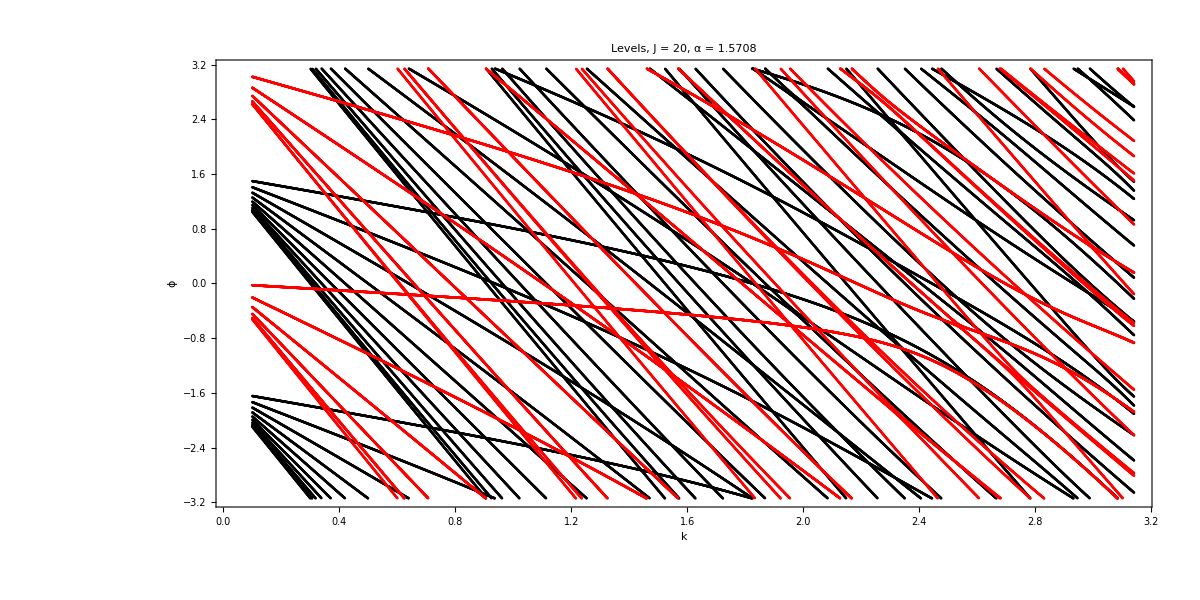

```mathematica
ListPlot[{Flatten[levelsm,1],Flatten[levelsM,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["ϕ",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
```

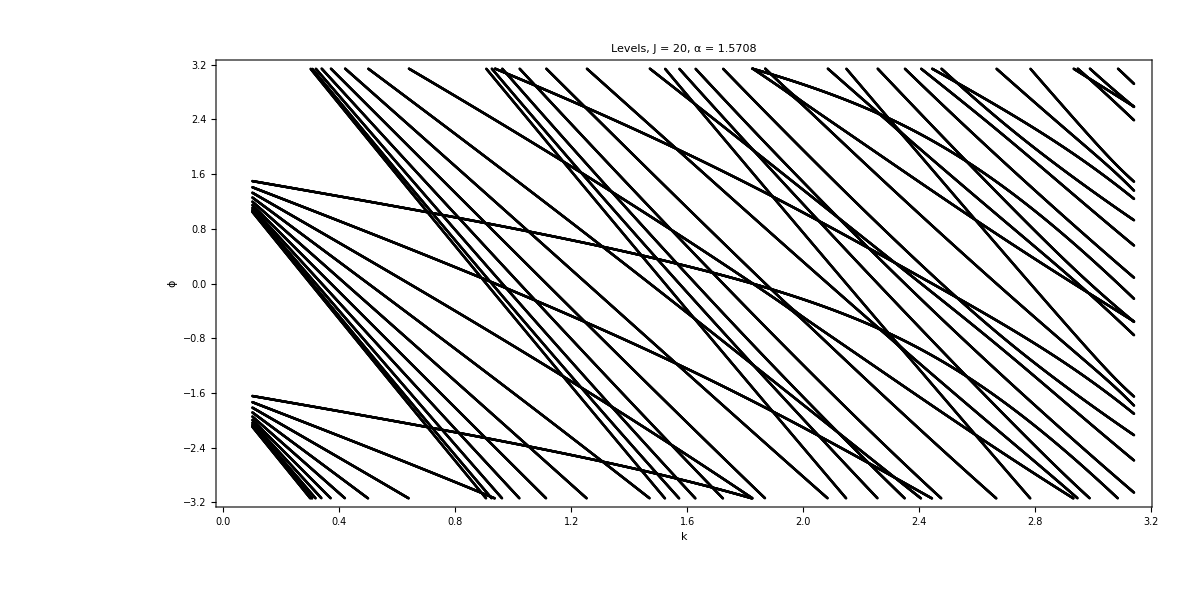

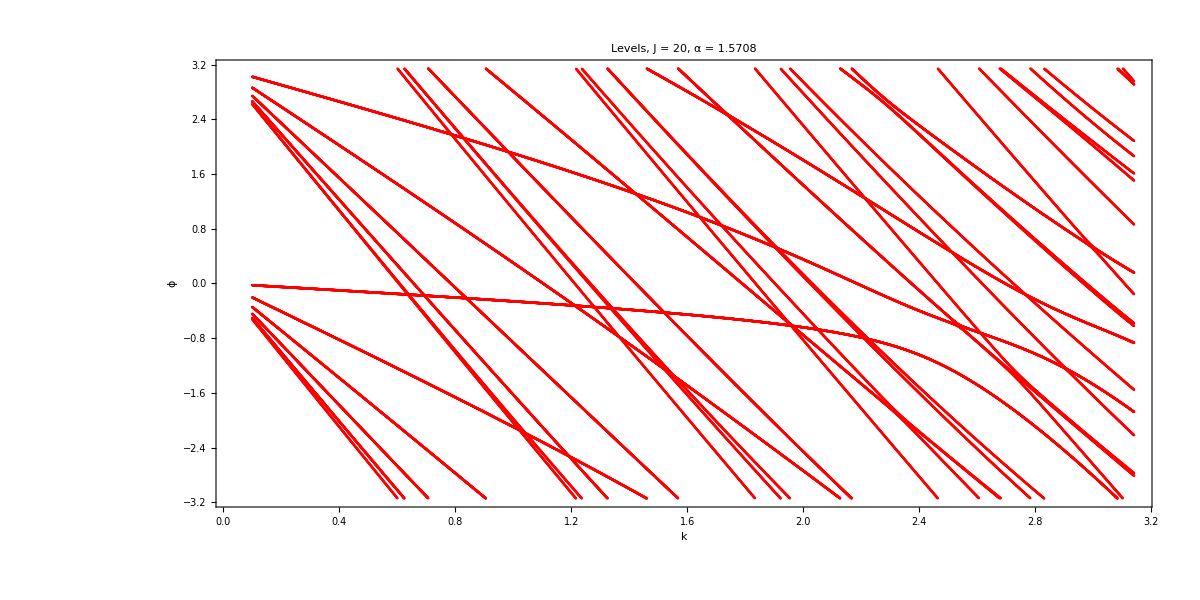

```mathematica
ListPlot[{Flatten[levelsm,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["ϕ",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
ListPlot[{Flatten[levelsM,1]},PlotStyle->{Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["ϕ",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
```

## Berry phases

```mathematica
resultsBerry=ParallelTable[Module[{mat,matM,matm,valM,valm,eigenvalM,eigenvalm,neweigenvecM,neweigenvecm,Vop,szM,szm,szExpectationsM,szExpectationsm,eigenvecM,eigenvecm},

data=GetQKTParityEigensystem[J,α,a];
{eigenvalM,eigenvalm}={data["Even","Quasienergies"],data["Odd","Quasienergies"]};
{eigenvecM,eigenvecm}={data["Even","Vectors"],data["Odd","Vectors"]};
{neweigenvecM,neweigenvecm}={data["Even","FullVectors"],data["Odd","FullVectors"]};

Vop=V[α,a];
{szM,szm}=SplitQKTParity[V[α,a]];
szExpectationsM=Chop[Map[ConjugateTranspose[#].szM.#&,eigenvecM]];
szExpectationsm=Chop[Map[ConjugateTranspose[#].szm.#&,eigenvecm]];

(*2. Calculate quasienergies (qe) for the corresponding eigenstates*)
qeM=Arg[eigenvalM];
qem=Arg[eigenvalm];
(*3. Calculate Berry phases:Mod[ae-qe,2*Pi]*)(*Note:If you prefer the phase to be wrapped between-Pi and Pi,you can use Mod[aeM-qeM,2 Pi,-Pi] instead*)
berryM=Mod[szExpectationsM-qeM,2 Pi];
berrym=Mod[szExpectationsm-qem,2 Pi];
(*4. Pair with the parameter'a' and sort the Berry phases for clean plotting*)
{Transpose[{ConstantArray[a,Length[berryM]],Sort[berryM]}],Transpose[{ConstantArray[a,Length[berrym]],Sort[berrym]}]}

],{a,alist},Method->"CoarsestGrained"];
```

```mathematica
(*Extract the two symmetry sectors*)
{levelsMBerry,levelsmBerry}=Transpose[Chop[resultsBerry]];
```

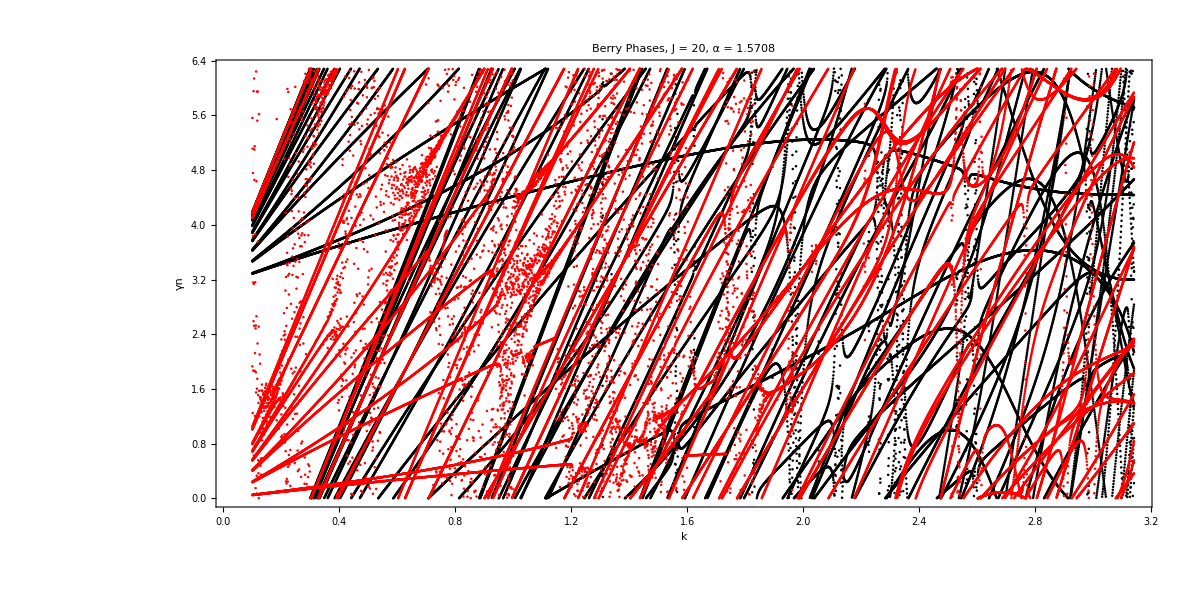

```mathematica
(*Plot the Berry Phases*)
ListPlot[{Flatten[levelsmBerry,1],Flatten[levelsMBerry,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["γn",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Berry Phases, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
```

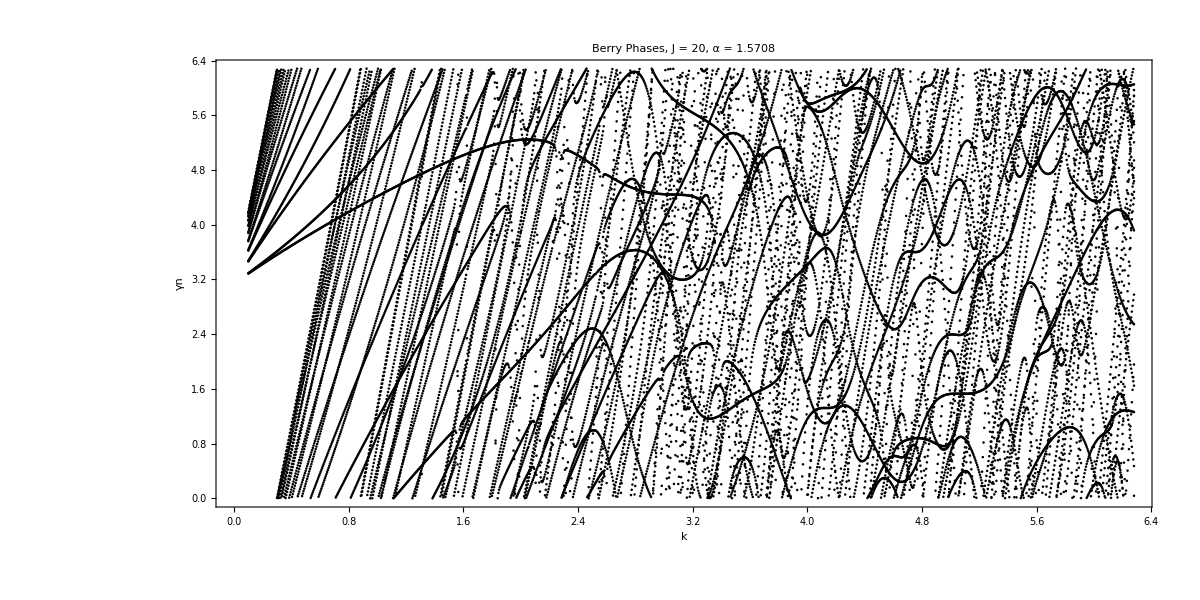

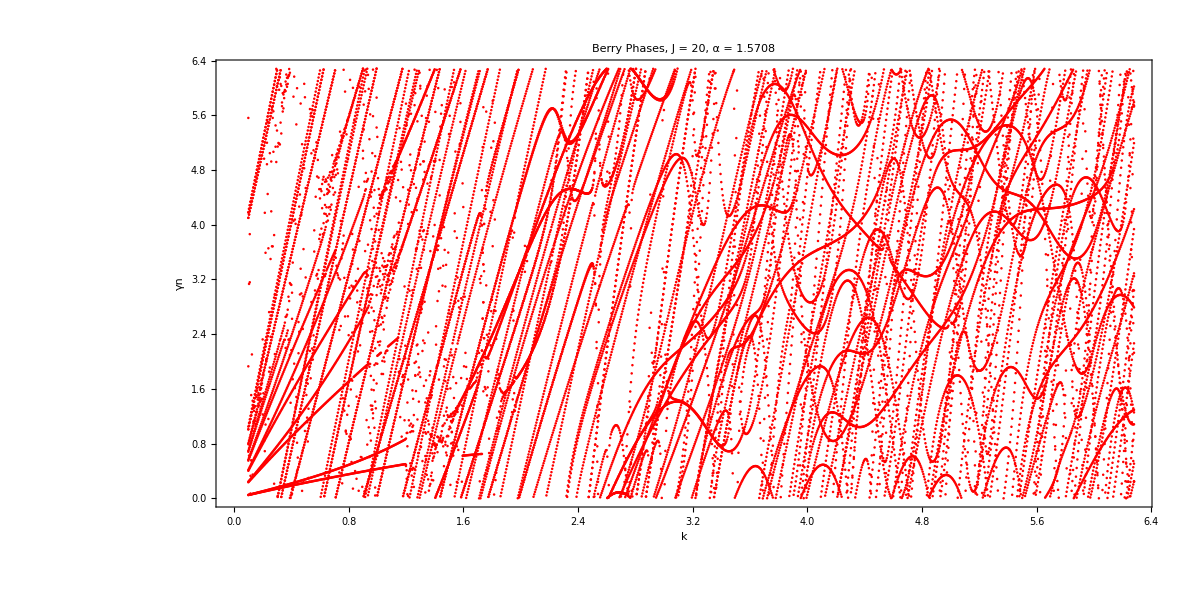

```mathematica
(*Plot the Berry Phases*)
ListPlot[{Flatten[levelsmBerry,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["γn",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Berry Phases, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
(*Plot the Berry Phases*)
ListPlot[{Flatten[levelsMBerry,1]},PlotStyle->{Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["k",30,Black],Style["γn",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Berry Phases, J = ",J,", α = "<>ToString[α]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
```

# Spectrum Hf as a function of α = π/2

## ae

```mathematica
(*Floquet parameters*)
J=40;
```

```mathematica
ops=generateSpinOperators[J];
(* Floquet: original with twist along Sz *)
Clear[Uk,U0,F];
Uk[k_] := MatrixExp[(-I k/(2 J)) ops[[4]]];
U0[α_] := MatrixExp[(-I α) ops[[3]]];
F[α_,k_] :=Uk[ k]. U0[α];
Clear[V];
V[α_,k_]:=(k/(2J))ConjugateTranspose[U0[α]].ops[[4]].U0[α]+α*ops[[3]];
```

```mathematica
α=Pi/2.;
```

```mathematica
Clear[SplitQKTParity];
SplitQKTParity[Op_?MatrixQ]:=Module[{dim,Jval,OpEven,OpOdd},
(*Calculate J from the dimension of the matrix (dim=2J+1)*)
dim=Length[Op];
Jval=(dim-1)/2;
If[EvenQ[Jval],
(*If J is EVEN:Row 1 (M=J) is Even Parity*)
OpEven=Op[[1;; ;;2,1;; ;;2]];
OpOdd=Op[[2;; ;;2,2;; ;;2]];,
(*If J is ODD:Row 1 (M=J) is Odd Parity*)
OpEven=Op[[2;; ;;2,2;; ;;2]];
OpOdd=Op[[1;; ;;2,1;; ;;2]];];
{OpEven,OpOdd}];
```

```mathematica
k=1.0;
```

```mathematica
data=GetQKTParityEigensystem[J,α,k];
{eigenvalM,eigenvalm}={data["Even","Quasienergies"],data["Odd","Quasienergies"]};
{eigenvecM,eigenvecm}={data["Even","Vectors"],data["Odd","Vectors"]};
{neweigenvecM,neweigenvecm}={data["Even","FullVectors"],data["Odd","FullVectors"]};
Vop=V[α,k];
{szM,szm}=SplitQKTParity[V[α,k]];
szExpectationsM=Chop[Map[#.szM.ConjugateTranspose[#]&,eigenvecM]];
szExpectationsm=Chop[Map[#.szm.ConjugateTranspose[#]&,eigenvecm]];
```

```mathematica
(*Assuming'qem' contains your real-valued quasienergies*)
tol=10^-8;
(*Group the phases where the cosine of their difference is-1*)
quasienergyPairs=Gather[Arg[eigenvalm],Cos[#1-#2]<-1+tol&];
(*Sort them cleanly*)
formattedPairs=SortBy[Map[Sort,quasienergyPairs],First];
```

```mathematica
formattedPairs
```

{{-3.04361,0.097979},{-2.66259,0.478999},{-2.33682,0.804773},{-2.18223,0.959366},{-1.59974,1.54185},{-0.911364,2.23023},{-0.480034,2.66156},{-0.369933,2.77166},{-0.18543,2.95616},{-0.112098,3.02949}}

```mathematica
ClearAll[calculateSectorDifferences];
(*Define a function that processes a single value of k*)
calculateSectorDifferences[J_,α_,k_]:=Module[{data,eigenvalm,eigenvecm,szM,szm,qem,szExpectationsm,berrym,indexedQEs,pairedIndices,diffQE,diffBerry,tol=10^-8},(*1. Diagonalize and fetch only the Odd (negative) sector*)
data=GetQKTParityEigensystem[J,α,k];
eigenvalm=data["Odd","Quasienergies"];
eigenvecm=data["Odd","Vectors"];
(*2. Safely calculate the pure-real expectation values*)
{szM,szm}=SplitQKTParity[V[α,k]];
szExpectationsm=Re[Map[ConjugateTranspose[#].szm.#&,eigenvecm]];
(*3. Calculate Quasienergies and Berry phases*)
qem=Arg[eigenvalm];
berrym=Mod[szExpectationsm-qem,2.0 Pi];
(*4. Attach an index to each quasienergy:{quasienergy,original_index}*)indexedQEs=Table[{qem[[i]],i},{i,Length[qem]}];
(*5. Gather the pairs using the Cosine trick on the first element (the quasienergy)*)pairedIndices=Gather[indexedQEs,Cos[#1[[1]]-#2[[1]]]<-1+tol&];
(*6. Loop through the paired sets and calculate the differences*)(*We use Select to ensure we only look at perfect pairs (length=2)*)
Map[Module[{qe1,qe2,idx1,idx2,b1,b2},
(*Extract the data from the gathered pair*)
qe1=#[[1,1]];idx1=#[[1,2]];
qe2=#[[2,1]];idx2=#[[2,2]];
(*Fetch the matching Berry phases using the saved indices*)
b1=berrym[[idx1]];
b2=berrym[[idx2]];
(*Calculate differences.We wrap Berry difference in Mod to keep it on the circle*)
diffQE=Abs[qe1-qe2];
diffBerry=Mod[Abs[b1-b2],2.0 Pi];
(*Return a clean data point:{k,δQE,δBerry}*)
{k,diffQE,diffBerry}]&,Select[pairedIndices,Length[#]==2&]]];
```

```mathematica
(*Parameters*)
J=20;
α=Pi/2;
kList=Range[0.1,Pi,0.002]; 
kList//Length
```

1521

```mathematica
(*Distribute the custom functions to the parallel workers*)
DistributeDefinitions[GetQKTParityEigensystem,SplitQKTParity,V,ops,U0,Uk,calculateSectorDifferences];
```

```mathematica
Print["Calculating pairs over k..."];
AbsoluteTiming[(*Run the sweep and flatten the sublists so we get one massive list of {k,dQE,dBerry}*)rawDifferencesData=Flatten[ParallelTable[calculateSectorDifferences[J,α,k],{k,kList},Method->"CoarsestGrained"],1];]
Print["Done!"];
```

Calculating pairs over k...

{1.69321,Null}

Done!

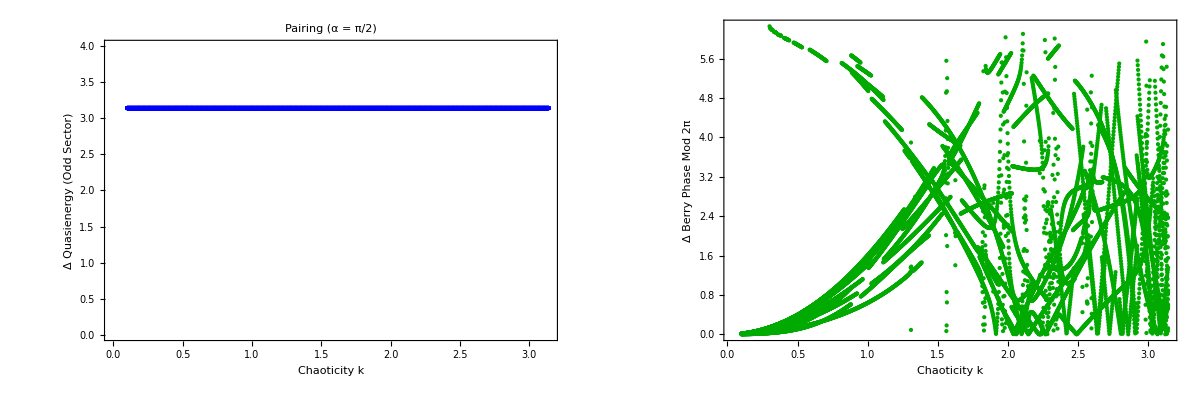

```mathematica
(*Extract the respective columns for the two plots*)
plotDataQE=rawDifferencesData[[All,{1,2}]];
plotDataBerry=rawDifferencesData[[All,{1,3}]];

(*Plot 1:Quasienergy Differences (Should be a flat line at Pi)*)
plotQE=ListPlot[plotDataQE,PlotStyle->Directive[Blue,PointSize[0.005]],PlotRange->{0,4},GridLines->{None,{Pi}},GridLinesStyle->Directive[Red,Dashed,Thickness[0.002]],Frame->True,FrameLabel->{"Chaoticity k","Δ Quasienergy (Odd Sector)"},PlotLabel->"Pairing (α = π/2)",BaseStyle->{FontFamily->"Helvetica",FontSize->14},ImageSize->600];

(*Plot 2:Berry Phase Differences*)
plotBerry=ListPlot[plotDataBerry,PlotStyle->Directive[Darker[Green],PointSize[0.005]],PlotRange->All,Frame->True,FrameLabel->{"Chaoticity k","Δ Berry Phase Mod 2π"},BaseStyle->{FontFamily->"Helvetica",FontSize->14},ImageSize->600];

(*Display them side by side*)
GraphicsRow[{plotQE,plotBerry},ImageSize->1200]
```

# Spectrum Hf as a function α

```mathematica
(*Floquet parameters*)
J=30;
```

```mathematica
ops=generateSpinOperators[J];
(* Floquet: original with twist along Sz *)
Clear[Uk,U0,F];
Uk[k_] := MatrixExp[(-I k/(2 J)) ops[[4]]];
U0[α_] := MatrixExp[(-I α) ops[[3]]];
F[α_,k_] := U0[α].Uk[ k];
Clear[V];
V[α_,k_]:=(k/(2J))ops[[4]]+α*ConjugateTranspose[Uk[k]].ops[[3]].Uk[k];
```

```mathematica
k=(2/5.)Pi*J;
```

```mathematica
alist=Range[0,2Pi,Pi/1000];
alist//Length
```

2001

```mathematica
zerosM=ConstantArray[0.,J];
zerosm=ConstantArray[0.,J+1];
```

```mathematica
DistributeDefinitions[Floq,J,k,MeanLevelSpacingRatio,V,zerosM,zerosm];
```

```mathematica
resultsae=ParallelTable[Module[{mat,matM,matm,valM,valm,eigenvalM,eigenvalm,neweigenvecM,neweigenvecm,Vop,szM,szm,szExpectationsM,szExpectationsm,eigenvecM,eigenvecm},
mat=Floq[J,a,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
{eigenvalM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{eigenvalm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];

Vop=V[a,k];
szM=(Vop)[[1;; ;;2,1;; ;;2]];
szm=(Vop)[[2;; ;;2,2;; ;;2]];
szExpectationsM=Map[#.szM.ConjugateTranspose[#]&,eigenvecM];
szExpectationsm=Map[#.szm.ConjugateTranspose[#]&,eigenvecm];

{Transpose[{ConstantArray[a,Length[szExpectationsM]],Sort[szExpectationsM]}],Transpose[{ConstantArray[a,Length[szExpectationsm]],Sort[szExpectationsm]}]}],{a,alist},Method->"CoarsestGrained" ];
```

```mathematica
CustomPiTicks[d_]:=Table[{k*Pi/d,If[k==0,"0",If[k==d,"",Row[{Rationalize[k/d],""}]]]},{k,0,2d+1}];
(*Generate ticks for Pi/xx*)
myTicks=CustomPiTicks[10];
```

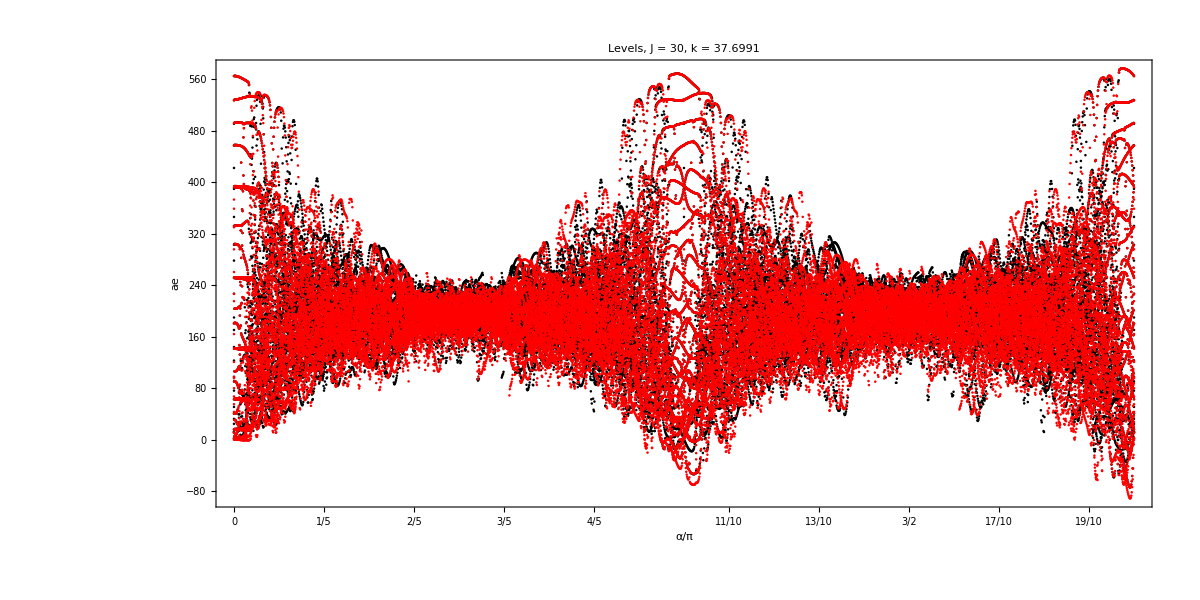

```mathematica
{levelsMae,levelsmae}=Transpose[Chop[resultsae]];
ListPlot[{Flatten[levelsmae,1],Flatten[levelsMae,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["α/π",30,Black],Style["ae",30,Black]},FrameTicks->{{Automatic,Automatic},{myTicks,Automatic}},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", k = "<>ToString[k]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
```

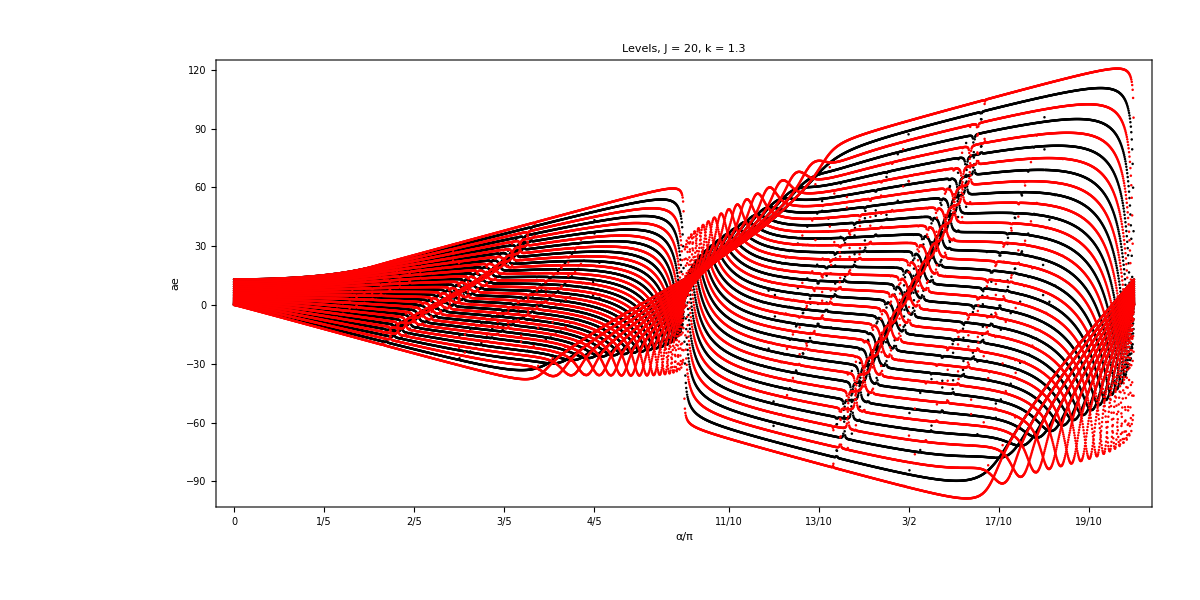

```mathematica
{levelsMae,levelsmae}=Transpose[Chop[resultsae]];
ListPlot[{Flatten[levelsmae,1],Flatten[levelsMae,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["α/π",30,Black],Style["ae",30,Black]},FrameTicks->{{Automatic,Automatic},{myTicks,Automatic}},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", k = "<>ToString[k]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
```

## Quasienergies

```mathematica
resultsphi=ParallelTable[Module[{mat,matM,matm,valM,valm},
mat=Floq[J,a,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
valM=Eigenvalues[matM];
valm=Eigenvalues[matm];
{Transpose[{ConstantArray[a,Length[valM]],Arg[valM]}],Transpose[{ConstantArray[a,Length[valm]],Arg[valm]}]}],{a,alist},Method->"CoarsestGrained" ];
{levelsM,levelsm}=Transpose[resultsphi];
```

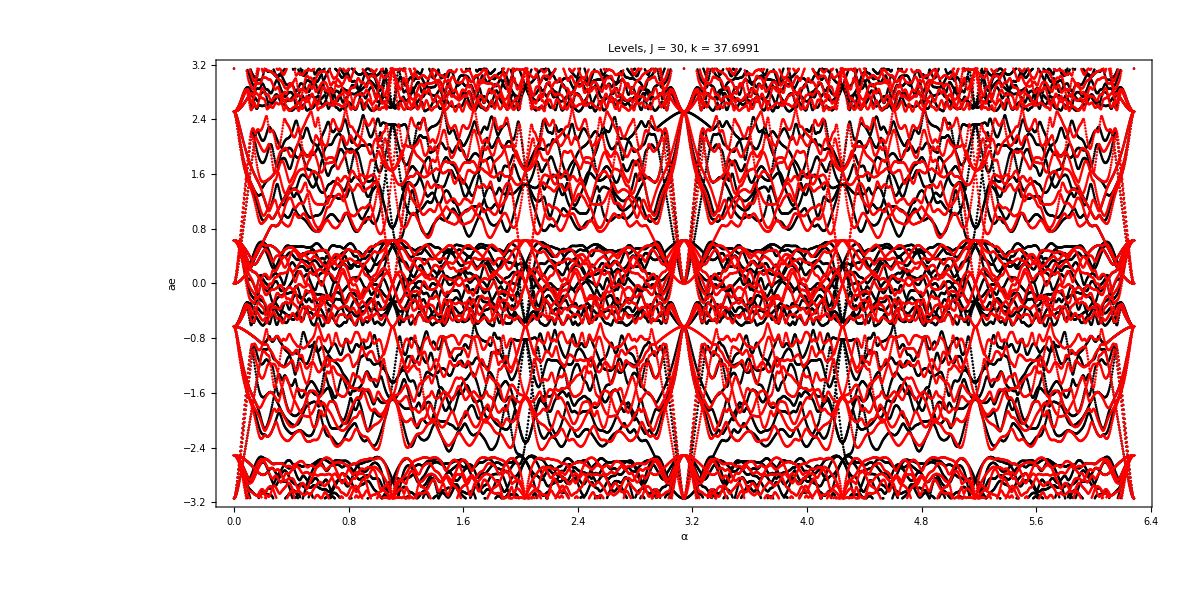

```mathematica
ListPlot[{Flatten[levelsm,1],Flatten[levelsM,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["α",30,Black],Style["ae",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Levels, J = ",J,", k = "<>ToString[k]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
```

## Berry phases

```mathematica
(*Calculate Berry Phases by combining AE and Quasienergy calculations*)
resultsBerry=ParallelTable[Module[{mat,matM,matm,valM,valm,eigenvecM,eigenvecm,Vop,szM,szm,aeM,aem,qeM,qem,berryM,berrym},
mat=Floq[J,a,k];
matM=mat[[1;; ;;2,1;; ;;2]];
matm=mat[[2;; ;;2,2;; ;;2]];
(*Get both eigenvalues and eigenvectors simultaneously to ensure they match*)
{valM,eigenvecM}=Eigensystem[matM,Method->"Direct"];
{valm,eigenvecm}=Eigensystem[matm,Method->"Direct"];
Vop=V[a,k];
szM=(Vop)[[1;; ;;2,1;; ;;2]];
szm=(Vop)[[2;; ;;2,2;; ;;2]];
(*1. Calculate average energies (ae) for each eigenstate*)
aeM=Chop[Map[#.szM.ConjugateTranspose[#]&,eigenvecM]];
aem=Chop[Map[#.szm.ConjugateTranspose[#]&,eigenvecm]];
(*2. Calculate quasienergies (qe) for the corresponding eigenstates*)
qeM=Arg[valM];
qem=Arg[valm];
(*3. Calculate Berry phases:Mod[ae-qe,2*Pi]*)(*Note:If you prefer the phase to be wrapped between-Pi and Pi,you can use Mod[aeM-qeM,2 Pi,-Pi] instead*)
berryM=Mod[aeM-qeM,2 Pi];
berrym=Mod[aem-qem,2 Pi];
(*4. Pair with the parameter'a' and sort the Berry phases for clean plotting*)
{Transpose[{ConstantArray[a,Length[berryM]],Sort[berryM]}],Transpose[{ConstantArray[a,Length[berrym]],Sort[berrym]}]}],{a,alist},Method->"CoarsestGrained"];
```

```mathematica
(*Extract the two symmetry sectors*)
{levelsMBerry,levelsmBerry}=Transpose[Chop[resultsBerry]];
(*Plot the Berry Phases*)
ListPlot[{Flatten[levelsmBerry,1],Flatten[levelsMBerry,1]},PlotStyle->{Directive[Black,PointSize[0.0015]],Directive[Red,PointSize[0.0015]]},Axes->False,Frame->True,FrameLabel->{Style["α",30,Black],Style["γn",30,Black]},GridLinesStyle->Directive[GrayLevel[0.8],Dashed],FrameStyle->Directive[Black,24,Thickness[0.0015]],LabelStyle->Directive[Black,24],PlotLabel->Style[Row[{"Berry Phases, J = ",J,", k = "<>ToString[k]}],25,Black],AspectRatio->0.5,ImageSize->1200,PlotRange->All]
```

# QKT Classic

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Geometric floquet\\QKT_full.wl"];
```

```mathematica
LaunchKernels[12]
```

{Local (12),Local (12),Local (12),Local (12),Local (12),Local (12),Local (12),Local (12),Local (12),Local (12),Local (12),Local (12)}

```mathematica
Names["QKT`*"]
```

{ClassicalMapeo,ClassicalStep,ClassicalToDisk,ClassicalToSphere,COEAsymptoticSigma2,COESFFAnalytical,CompileLevelCounter,CompileSFF,ComputeSigma2Sliding,EnsembleSFF,EnsembleSigma2,EvaluateSpectrumSigma2,Floq,Floqb,Floqbn,Floqn,Floqsym,FluctuationPowerSpectrum,GenerateCOEEnsemble,generateCoherentStateCompiler,GenerateQKTEnsemble,generateSpinOperators,GetFluctuations,GetQKTParityEigensystem,GetQKTParitySpectra,IntWignerCOE,IPR,LengthSpectrum,MeanLevelSpacingRatio,NNSpacings,ParitySectorIndices,PoolSpacingRatios,PoolSpacings,PrCOE,PrCUE,PrPoisson,RandomCOESpectrum,SingleSFF,SingleSpectrumSigma2,UnfoldLinear,ValidateUnfolding,WignerCOE}

## Computations

```mathematica
(*Execution*)
α=0.84;
k=3.;
kicks=2000;
(*Random inintial conditions on the disk/phase space*)
points=300;
randomregion=RandomPoint[Disk[{0,0},1.99],points];
```

```mathematica
(*The'Listable' attribute handles the parallel iteration over'randomregion' automatically*)
result=ClassicalMapeo[randomregion,α,k,kicks,0];
```

```mathematica
newpoincarea=ArrayReshape[result,{points*kicks,2}];
poincare=ListPlot[newpoincarea,PlotStyle->Directive[PointSize[0.0005],Black,Opacity[0.15]],PlotLabel->Row[{Style["α = ",35,Black],Style[N[α],35,Black],Style[", k = ",35,Black], Style[N[k],35,Black],Style[" (rotation-kick)",24,Black]}],FrameLabel->{Style["Q",30,Black],Rotate[Style["P",30,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,PlotRange->{{-2,2},{-2,2}},ImageSize->1000]
```

-Graphics-

```mathematica
Export["poincareplot.png",poincare,ImageResolution->300]
```

poincareplot.png